```mathematica
MeasurementUp=({{2.11, 0}, {2.84, 0.01}, {3.01, 0.01}, {3.09, 0.01}, {3.21, 0.01}, {3.33, 0.02}, {3.46, 0.02}, {3.56, 0.02}, {3.65, 0.02}, {3.79, 0.02}, {3.87, 0.03}, {3.96, 0.03}, {4.05, 0.04}, {4.16, 0.05}, {4.27, 0.06}, {4.36, 0.07}, {4.45, 0.08}, {4.57, 0.12}, {4.68, 0.15}, {4.78, 0.16}, {4.89, 0.16}, {4.99, 0.16}, {5.08, 0.16}, {5.19, 0.18}, {5.30, 0.18}, {5.38, 0.19}, {5.47, 0.20}, {5.55, 0.19}, {5.70, 0.21}, {5.82, 0.19}, {5.95, 0.26}, {6.16, 0.29}, {6.29, 0.37}, {6.43, 0.42}, {6.54, 0.46}, {6.69, 0.48}});
MeasurementDown=({{6.46, 0.30}, {6.28, 0.27}, {6.22, 0.25}, {5.98, 0.18}, {5.79, 0.17}, {5.72, 0.15}, {5.53, 0.12}, {5.42, 0.12}, {5.25, 0.11}, {4.97, 0.08}, {4.78, 0.07}, {4.55, 0.05}, {4.32, 0.04}, {4.12, 0.03}, {3.86, 0.03}, {3.53, 0.02}, {3.28, 0.01}, {3.05, 0.01}, {2.77, 0}});
```

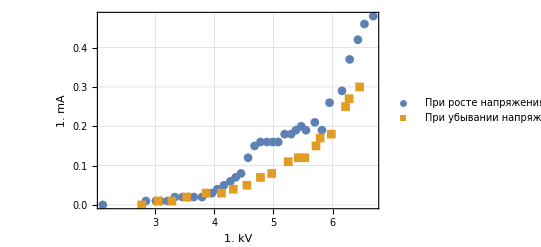

```mathematica
ListPlot[{MeasUp,MeasDown},PlotTheme->"Detailed",PlotLegends->Placed[{"При росте напряжения", "При убывании напряжения"},Above],Frame->True,FrameLabel->{MeasUp[[1,1]]/QuantityMagnitude[MeasUp[[1,1]]],MeasUp[[2,2]]/QuantityMagnitude[MeasUp[[2,2]]]},PlotMarkers->Automatic]
```

```mathematica
MeasUp=MeasurementUp;
MeasDown=MeasurementDown;
For[i=1,i≤Length[MeasurementUp],i++,
MeasUp[[i,1]]=Quantity[MeasUp[[i,1]],"Kilovolts"];
MeasUp[[i,2]]=Quantity[MeasUp[[i,2]],"Milliamperes"];
]
For[i=1,i≤Length[MeasurementDown],i++,
MeasDown[[i,1]]=Quantity[MeasDown[[i,1]],"Kilovolts"];
MeasDown[[i,2]]=Quantity[MeasDown[[i,2]],"Milliamperes"];
]
```

```mathematica
FNUp=Transpose[Append[{1/MeasUp[[All,1]]},Log[QuantityMagnitude[MeasUp[[All,2]]/MeasUp[[All,1]]^2]]]];
FNDown=Transpose[Append[{1/MeasDown[[All,1]]},Log[QuantityMagnitude[MeasDown[[All,2]]/MeasDown[[All,1]]^2]]]];
```

```mathematica
FNU=LinearModelFit[QuantityMagnitude[FNUp[[2;;All]]],x,x]
FND=LinearModelFit[QuantityMagnitude[FNDown[[1;;Length[FND]-2]]],x,x]
```

FittedModel[-2.62781-13.0043 x]

FittedModel[-2.4037-16.3225 x]

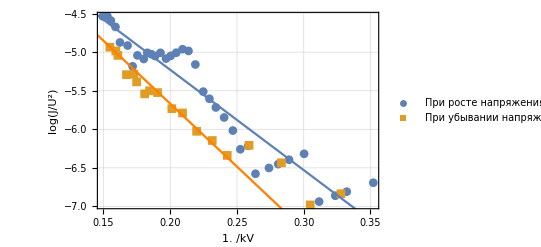

```mathematica
Show[ListPlot[{FNUp,FNDown},PlotTheme->"Detailed",PlotLegends->Placed[{"При росте напряжения", "При убывании напряжения"},Above],Frame->True,FrameLabel->{FNDown[[1,1]]/QuantityMagnitude[FNDown[[1,1]]],Log[J/U^2]},PlotMarkers->Automatic,PlotRange->Full],Plot[FNU["BestFit"],{x,0.14,0.4}],Plot[FND["BestFit"],{x,0.14,0.4},PlotStyle->Orange]]
```